## Preamble

### Initialization

Follow the instructions on BB for installation and connecting to the Mathematica license server (note that you must be connected to NTNU’s IP domain (on campus or via VPN).

Load the StateDiagrams.m package (change the directory to the folder you are using) [developed by prof.em. Bjarne E. Helvik, NTNU]

```mathematica
(* Set the current directory to the directory/folder where you have stored the "StateDiagrams_mma-v12.m"-file *)
(* SetDirectory[$YOURDIRECTORY]*)
(** EXAMPLE ON POUL'S COMUPTER - you must change this **)
SetDirectory[$HomeDirectory];
SetDirectory["/Users/HEMMELIG(good catch??.af\_(ツ)_/.af)/Desktop/efefef/TTM4110/Labs/LAB III"];
```

Import and list of the available functions in the package

```mathematica
Import["StateDiagrams_mma-v12.m"];
Names["Dependability`StateDiagrams`*"]
```

{ArrangeMatrix,DownTimeDensity,DownTimeDensityLaplace,GenHomogeneousSystem,KoutofN,KoutofNMode,KroenSum,LabelList,MDT,MergeStates,MTBF,MTFF,MTTF,MUT,ParallelMode,PlotDiagram,ProbStationary,ProbTransient,RelFunc,SeriesMode,SetDiagonal,StepPlot,UnAvailability}

### Examples of use: Markov model of a network element with two states [Up (1) /Down (0)]

#### Define a transition intensity matrix

```mathematica
Subscript[μ, 1]=.
```

```mathematica
𝒬=Table[",",{2},{2}]; 
(* assign intensities to all transitions, null to non-transitions *) 
𝒬[[1,2]]=Subscript[λ, 1]; (* assign failure rate *)
𝒬[[2,1]]=Subscript[μ, 1];(* assign repair rate *)
Subscript[ℳ, 1]= SetDiagonal[Transpose[𝒬]];(* add the diagonal elements, see Sect 5.2.4 *)
Subscript[ℳ, 1]//MatrixForm  (* Print nicely on matrix form *)
MatrixForm[Subscript[ℳ, 1]]  (* Print nicely on matrix form *)
```

(-λ_1 | μ_1
λ_1 | -μ_1)

(-λ_1 | μ_1
λ_1 | -μ_1)

#### Label two states

```mathematica
(* Label the states -  note that the states in the printed diagram is alphabetiallcy order! *) 
Subscript[ℒ, 1]={0,1};
Subscript[𝒯, 1]={"0:Up","1:down"};
```

```mathematica
{0,1}
```

{0,1}

#### Plot the diagram as defined - compare with figure above

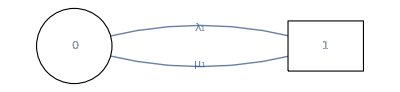

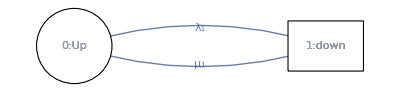

-Graphics-

```mathematica
(* Define operation modus of the two states.
True=up/working, False=down/failed in dependability models, and True for all states in a performance model *)
Subscript[𝒲, 1]={True,False};  
PlotDiagram[Subscript[ℳ, 1],Subscript[𝒲, 1],Subscript[ℒ, 1]]
(* alternative labels *)
PlotDiagram[Subscript[ℳ, 1],Subscript[𝒲, 1],Subscript[𝒯, 1]]
(* with all states True *)
Subscript[𝒲, 2]={TrueTrue};
(* The states in the printed diagram is alphabetiallcy order, but the order of states in the Subscript[ℳ, 1] and Subscript[𝒲, 1] are unchanged! *)
PlotDiagram[Subscript[ℳ, 1],Subscript[𝒲, 2],{"up","down"}]
```

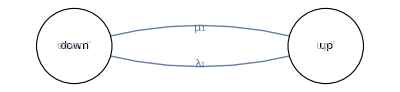

#### Determine the transient and steady state probabilities

```mathematica
(* transient probabilities, defined a function of t - ":=" means assign a function, and t_ defines a write protected variable *)
(*psT[t] (* show the funtion *)*)
psT[t_,ℳ_,init_]:=ProbTransient[ℳ,init,t]
(* steady state probabilities *)
ps = ProbStationary[Subscript[ℳ, 1]]
(* As a function : *)
psS[ℳ_] := ProbStationary[ℳ]
psS[Subscript[ℳ, 1]]
```

LinearSolve[{{-α-λ,α,λ,0,0,0,0,0,0,0,0,0,0,0},{β,-β-λ,0,λ,0,0,0,0,0,0,0,0,0,0},{0,0,-α-λ,α,λ,0,0,0,0,0,0,0,0,0},{0,μ,β,-β-λ-μ,0,λ,0,0,0,0,0,0,0,0},{0,0,0,0,-α-λ,α,λ,0,0,0,0,0,0,0},{0,0,0,μ,β,-β-λ-μ,0,λ,0,0,0,0,0,0},{0,0,0,0,0,0,-α-λ,α,λ,0,0,0,0,0},{0,0,0,0,0,μ,β,-β-λ-μ,0,λ,0,0,0,0},{0,0,0,0,0,0,0,0,-α-λ,α,λ,0,0,0},{0,0,0,0,0,0,0,μ,β,-β-λ-μ,0,λ,0,0},{0,0,0,0,0,0,0,0,0,0,-α-λ,α,λ,0},{0,0,0,0,0,0,0,0,0,μ,β,-β-λ-μ,0,λ},{0,0,0,0,0,0,0,0,0,0,0,0,-α,α},{0,0,0,0,0,0,0,0,0,0,0,μ,β,-β-μ}}_{1,1},{0,1}]

LinearSolve[{{-α-λ,α,λ,0,0,0,0,0,0,0,0,0,0,0},{β,-β-λ,0,λ,0,0,0,0,0,0,0,0,0,0},{0,0,-α-λ,α,λ,0,0,0,0,0,0,0,0,0},{0,μ,β,-β-λ-μ,0,λ,0,0,0,0,0,0,0,0},{0,0,0,0,-α-λ,α,λ,0,0,0,0,0,0,0},{0,0,0,μ,β,-β-λ-μ,0,λ,0,0,0,0,0,0},{0,0,0,0,0,0,-α-λ,α,λ,0,0,0,0,0},{0,0,0,0,0,μ,β,-β-λ-μ,0,λ,0,0,0,0},{0,0,0,0,0,0,0,0,-α-λ,α,λ,0,0,0},{0,0,0,0,0,0,0,μ,β,-β-λ-μ,0,λ,0,0},{0,0,0,0,0,0,0,0,0,0,-α-λ,α,λ,0},{0,0,0,0,0,0,0,0,0,μ,β,-β-λ-μ,0,λ},{0,0,0,0,0,0,0,0,0,0,0,0,-α,α},{0,0,0,0,0,0,0,0,0,0,0,μ,β,-β-μ}}_{1,1},{0,1}]

### Some useful functions

General advise: check the help pages - good descriptions and many examples

```mathematica
(* Ex: how to plot? click (i)-symbol for more info 
You can also use "mouse over" for drop down menu *)
?Plot
```

General advise : check for shortcuts (https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html )

```mathematica
(* Evaluate notebook - [shift]+[crt]*)
(* Latex code : CTRL-4 -> add latex code (ex \sim = )*)
(* [shift]+_ -> subscript : A[shift]+_1 = Subscript[A, 1] *)
```

Probability distributions:

```mathematica
(* Gaussian / Normal-distribution *)
(* NOTE when you add ; at the end of line you evaluate the expression but don't print it *)
Subscript[𝒟, ex]= NormalDistribution[a,b];
para={a->1,b->0.5};
Mean[Subscript[𝒟, ex]]
Variance[Subscript[𝒟, ex]]
(* probability density function *)
PDF[Subscript[𝒟, ex],t]
(* as a function *) 
Subscript[f, ex][t_] := PDF[Subscript[𝒟, ex],t];
(* assing temporar values to the parameter *)
(* /. means "apply rule" *)
 Subscript[f, ex][t] /. para
(* cummulative distribution function *)
Subscript[F, ex][t_]:=CDF[Subscript[𝒟, ex],t]
(* plot both - Plot has a LOT of parameters .. check help *) 
Plot[{Subscript[f, ex][t] /.  para,
Subscript[F, ex][t] /.  para},
{t,-1,4}, PlotLabels->{pdf,cdf}]
```

a

b^2

(ⅇ^(-(-a+t)^2/(2 b^2)))/(b √(2 π))

0.797885 ⅇ^(-2. (-1+t)^2)

CompiledFunction::cfsa: Argument a at position 2 should be a machine-size real number.

-Graphics-

## Lab III: Smart City Bus Transportation System

### System description

See assignment text lab I/II for details about the system.

### Task III.A: Bus arrivals and number of passengers at a bus stop

In this part of the assignment we consider only one bus stop. 
To estimate the expected number of passengers at a bus stop we need to obtain the probability that a bus is at the bus stop and the probability that x passengers are at a bus stop.

Assume the following (time unit is minute - in some tasks the parameter values might change): 
- Arrivals of busses to a bus stop is according to a Poisson process, with intensity α, (α=0.2)
- The  time a bus stays at the bus stop is negative exponentially distributed with expected time 1/β (β=1)
- Passengers arrive at a bus stop according to a Poisson process, with intensity λ, (λ=1.2)
- The time to enter the bus for a passenger is negative exponentially distributed with expected time 1/μ (μ=10)
(In Mathematica you can define this in a (rule) set:  𝒫_1 = {λ->1.2,μ->10,α->0.2,β->1};)

#### Task III.A.1

Passengers arrive at a bus stop with an intensity λ, according to a Poisson process.  
a) Write the symbolic expression of the probability density function of the inter-arrival time of T_p,  passengers.
b) What is this distribution called? 
c) Give a symbolic expression of the expectation and standard deviation of T_p.  
d) Do this on paper first (find the expressions in the textbook), and then explore how you can do this in Mathematica (use the built in functions).
e) Write the  symbolic expression of the probability of i passenger arrivals in time interval (0,τ) (Symbolically).  What is this distribution called?
f) What is the probability that 5 passengers arrive in τ? (τ->5)
g) What is the expected number of passenger arrivals in τ? (τ->5) (Symbolically and numerically)
h) What is the probability that a bus will arrive later than  τ? (τ->5) (Symbolically and numerically)
[Chapter 2 in the textbook].

a) The symbolic expression of the probability density function of the inter-arrival time of is:
	
	
b) This distribution is called an exponential distribution.

c) The expectation of :
	
    The standard deviation of :
    	
    	
d) Expressions in Mathematica below:

```mathematica
Clear[λ, t]

distribution = ExponentialDistribution[λ];

PDF[distribution, t]
Mean[distribution] 
StandardDeviation[distribution]
```

Piecewise[{{ⅇ^(-t λ) λ, t≥0}, {0, True}}]

1/λ

1/λ

e) The symbolic expression for the probability of i passenger arrivals in time interval (0,τ) is given by

```mathematica
f[N[τ_]==i_]:=(((λ*τ)^i)*Exp[-λ*τ])/i!
```

This is the Poisson distribution with rate , where  is the expected number of arrivals in time .

f) By using the equation in e), we can calculate that the  probability of 5 passengers arriving in time  = 5 is

```mathematica
i = 5;
τ = 5;
λ = 1.2;

f[N[τ]=i]
```

0.160623

g) The expected number of arrivals in a Poisson process is given by
	
     By using the equation above we can calculate that the expected number of passengers in time  = 5 is

```mathematica
expected[τ_] = λ*τ
```

6.

h)   The probability that the inter-arrival time ​ is greater than  can be calculated using the survival function of the exponential distribution
	
      By using the equation above we can calculate that the probability that the bus arrives later than τ = 5 is

```mathematica
P = Exp[-τ*λ]
```

0.00247875

#### Task III.A.2

The expected time T_b between bus arrivals to a bus stop is 1/α  (i.e., T_b n.e.d.(α)). 
a) What is the first and second order moments of T_b? (Symbolically)
Assume that a passenger arrives a bus stop at specific time u.  
b) What is the probability distribution and the expected value of the waiting time (until the next bus) from time u?  (Symbolically)
c) What is the probability distribution and the expected value of the waiting time if the passenger arrives at a random point in time? (Symbolically)
d) Comment on the different expressions.

a) From statistics we know that the first order moment is equal to the expected value. Using Mathematica to calculate first and second order moments:

```mathematica
Clear[α]
dist = ExponentialDistribution[α];
firstMomentTb=Mean[dist]
secondMomentTb=Moment[dist,2]
```

1/α

2/α^2

b) Time between bus arrivals follows an exponential distribution with a parameter α, since the bus follows a Poisson process. Distribution and expected value is calculated using Mathematica below.

```mathematica
pdfWaitingTime = PDF[dist, u]
expectedValue = Mean[dist]
```

Piecewise[{{ⅇ^(-u α) α, u≥0}, {0, True}}]

1/α

c) When the passenger arrives at a random time, the distribution and the expected value remains the same as in b),  because of the memoryless property of the exponential distribution.

d) Expressions have been commented above.

#### Task III.A.3*

Now, let T_b Erlang(k,k α), an Erlang distribution with shape parameter k and rate kα.
a) What is the expected value, and the first and second order moments of T_b . (Symbolically)
b) Obtain the expected value of the forward recurrence time.  (Symbolically)
c) Comment on the different expressions, and compare with the expected forward recurrence time of  T_b n.e.d.(α) from III. 2.  (Symbolically)
d) Let k=1, and obtain the expected value of the forward recurrence time.  Comment on the result.

a) Using built-in function gives the first and second order moments of

```mathematica
erlangDist=ErlangDistribution[k,k*α];
firstMomentErlang=Moment[erlangDist,1]
secondMomentErlang=Moment[erlangDist,2]
```

1/α

(1+k)/(k α^2)

b) The forward recurrence time (FRT) can be calculated using the first and second order moments of . The formula for expected FRT is:
	
     Calculated below using Mathematica:

```mathematica
ErlangForwardRecurrenceTime = secondMomentErlang / (2*firstMomentErlang)
```

(1+k)/(2 k α)

c) The Erlang distribution generalizes the exponential distribution. While the exponential random variable describes the time between adjacent events, the Erlang random variable describes the time interval between any event and the th following event.

```mathematica
ExponentialFRT = secondMomentTb / (2 * firstMomentTb)
```

1/α

When comparing the Erlang FRT to the exponential FRT, we can see that when  increases, the FRT. increases. This is because the Erlang distribution models a process where  events are required to occur before a bus arrives, which increases the expected waiting time compared to the simple exponential case.

d) When  the Erlang distribution simplifies to the exponential distribution and we get the same FRT as for the exponential distribution. This shows once again that the FRT for an exponential distribution is simply , which makes sense given the memoryless property of the distribution, where the expected time stays the same regardless of when you start counting.

```mathematica
k= 1;
ErlangForwardRecurrenceTime
```

1/α

#### Task III.A.4

The expected time T_b between bus arrivals to a bus stop is 1/α  (T_b n.e.d.(α)), and the expected time T_s a bus is at the bus stop is 1/β  (T_s n.e.d.(β)). 
Assume that the time at a bus stop is independent of the number of passengers waiting.  
a) What is the probability that a bus is at the bus stops? [hint: you can make a two state Markov model].

a) First calculated by hand, and then with Mathematica below.

We introduce two states: 
	State 1 ( ): Bus at the bus stop
	State 2 (): Bus not at the bus stop
	
The given rate for buses to arrive at a bus stop is 
The given rate for busses to leave the bus stop is 

Since the system is a Markov chain, the sum of the probabilities must add up to 1: 
	   (1)
	
Balance equations for the two states: 
	    (2)

If we write  as a function of :
	    (2)
	
Substitute this into (1):
	 
	
	
And  solve for  :
	 
	
We get that the probability that the bus is at the bus stop is:

{{π1→0.166667,π2→0.833333}}

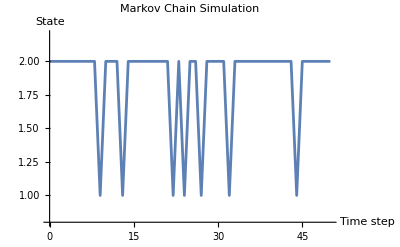

```mathematica
ClearAll[α,β, P]
α = 0.2;
β = 1;
P = {{1 - β, β }, {α, 1 - α}}; (*Transition Matrix*)
steadyState = Solve[{π1 (1 - β) + π2 * α  == π1, π1 * β + π2 *(1 - α) == π2, π1  + π2 == 1}, {π1, π2} ]

markovProcess = DiscreteMarkovProcess[2, P] (*Starting in State 2*);
simulation = RandomFunction[markovProcess, {0, 50}];

ListPlot[simulation["Path"], Joined->True, 
PlotRange->{0.8, 2.2}, 
AxesLabel->{"Time step", "State"}, 
PlotLabel->"Markov Chain Simulation"]
```

Here is the Markov Chain for bus arrival/departure. State 1 means bus at the stop, and State 2 means bus not at the stop. The system starts at State 2, and switches between the two states with random time intervals. When the bus arrives at a stop (switches from state 2 to 1), it leaves right away (switches back).

#### Task III.A.5*

We know that the arrival rate of a bus is a constant α, and time between busses are i.i.d (independent, identically distributed).  Then, the time between busses are T_b f_α(t), where f_α(t) is the negative exponential distribution (i.e., T_b n.e.d.(α)).  
Now, let  f_α(t) instead be an Erlang-k distribution with expectation 1/α, where α = 10. 
a) Use the built in function in Mathematica, and plot the arrival rate ϕ(t) as a function of t with scale values k=1, 3 , 5, 10 .  
b) Comment on the differences in ϕ(t) for the different k-values , and in particular the k=1. 
c) Reflection: if you section the road between two bus stops in k sections (of equal driving time),  what is the pdf of each section if the total driving time is f_α(t)=Erlang(α,k).
[Chapter 2 and 3 in the textbook].

a) The definition rate of  is defined as 
	
     where   is the PDF for time  and  is the CDF for  time .
      is plotted below;

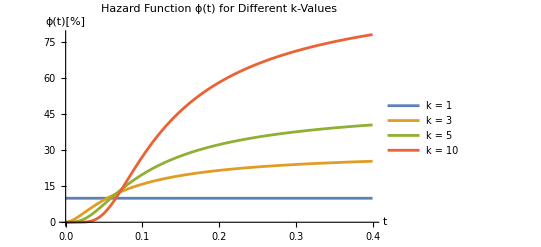

```mathematica
Erlang[k_,α_]:=ErlangDistribution[k,k α]
ErlangPDF[k_,α_,t_]:=PDF[Erlang[k,α],t]
ErlangCDF[k_,α_,t_]:=CDF[Erlang[k,α],t]
Clear[α]
α=10;
kVals={1,3,5,10};

ϕ[k_,α_,t_]:=ErlangPDF[k,α,t]/(1-ErlangCDF[k,α,t])

start=0;
end=0.4;

Plot[
Evaluate[Table[ϕ[k,α,t],{k,kVals}]],
{t,start,end},
PlotLegends->{"k = 1","k = 3","k = 5","k = 10"},
AxesLabel->{"t","ϕ(t)[%]"},
PlotLabel->"Hazard Function ϕ(t) for Different k-Values"
]
```

b) The plot above shows ϕ(t) of Erlang distributions for different values of . We know that the Erlang distribution simplifies to the exponential distribution when . For this case,  is constant because of the memoryless property of the exponential distribution, meaning  the likelihood of events are independent of each other. Another remark is that as  increases,  increases more rapidly. This is because of properties of the Erlang distribution saying that an event becomes more likely after a certain amount of waiting time. Larger values of  represents more stages that the process needs to complete, and because of this the time of bus arrivals gets more predictable.

c) If we were to divide the road between two bus stops into  sections, with the total travel time  f_α(t)=Erlang(α,k), each section is one “stage” of the Erlang process (k += 1). Since the total travel time between the bus stops follows an Erlang distribution, the driving time for each of the  sections will follow an exponential distribution. This is because the Erlang dist, is the sum of  exponentially distributed stages, where each section has its own exponential waiting time with rate . The PDF for each section is given by:

### Task III.B: Markov model of a bus stop

A passenger can only enter the bus when the bus is at the bus stop.  In this part of the lab we are going to make and compare three different Markov models that can be used to determine the probability of i passenger at a bus stop (and hence, also the expected number of passengers).

#### Task III.B.1

The time T_p between arrivals of passengers to a bus stop is i.i.d, with intensity λ_p, T_p n.e.d.(λ_p). The time for a passenger to enter the bus is i.i.d, with rate μ_p per passenger, T_e n.e.d.(μ_p)  (given that the bus is there).  From III.A.4, we know that the probability of a bus at a bus stop is p_s.  
[[Do this assignment first on paper, and if you want you can also use QueuingProcess in Mathematica to check your calculations.]]
a) Determine the average service rate (Μ) per passenger, when μ_p is the service rate per passenger when the bus is at the bus stop, and 0 otherwise.  (symbolically, and numerically using 𝒫_𝒬={λ_p->0.2,μ_p->2,α->0.2,β->1.2}).
b) Your objective is to estimate the expected waiting time at a bus stop. Define descriptive state variable(s), identify events that changes the state, and make a Markov model. 
c) What kind of queuing model is this if we assume no limitation of the space at the bus stop so all passengers who want can wait there (use Kendall’s notation).
d) Obtain the mean number of passengers, E[S], and the mean passenger waiting time at bus stop, E[W].
e) What is the probability of m(=6) or more passengers waiting at a bus stop? 
f) Plot the probability (e.g., ListLinePlot, BarPlot) of 0-m passengers
[Chapter 5 and 6 in the textbook]

a) Service rate per passenger when the bus is at the stop is  . When there is no bus, the service rate  is  . From III.A.4 we have that an equation for the probability of a bus being at a stop denoted as  . Therefore, the average service rate per passenger, , will depend on whether the bus is there or not.

0.285714

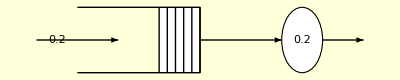
-Graphics- | 
Basic Properties | 
QueueNotation | M/M/1
ArrivalRate | 0.2
ServiceRate | 0.285714
UtilizationFactor | 0.7
Throughput | 0.2
ServiceChannels | 1
SystemCapacity | ∞
InitialState | 0
Performance Measures | 
MeanSystemSize | 2.33333
MeanSystemTime | 11.6667
MeanQueueSize | 1.63333
MeanQueueTime | 8.16667

```mathematica
ClearAll[λ,μ,α,β, M, queue]
Subscript[𝒫, Q] = {λ->0.2,μ->2,α->0.2,β->1.2};
busProb  = α/(α+β);
M =busProb μ/. Subscript[𝒫, Q]

queue =  QueueingProcess[λ, M, 1]/. Subscript[𝒫, Q];
QueueProperties[queue]/. Subscript[𝒫, Q]
```

b) We have two key events: arrival of passengers  (λ) and service of passengers (μ). Therefore, the state variable can be defined as the number of passengers waiting at the bus stop at time  defined as . Markov model is illustrated below;

c) M/M/1//FIFO

d) Expected number of customers in an M/M/1 system is given by
	
     
     where .
     
     Expected waiting time for all customers in an M/M/1 system can be calculated by applying Little’s formula to the queue
     	
     	
     	
     where .
     In our case .

```mathematica
A =λ/M /. Subscript[𝒫, Q];
expecNumPass  = A / (1 - A)
expecPassWaitTime = A/((1-A) ) /. Subscript[𝒫, Q]
```

2.33333

11.6667

We can see that the mean number of passenger is , and that the mean passenger waiting time is  .

e) Probability of  . . Possibility of  passengers in an M/M/1 system is given by
	.

```mathematica
Clear[i];
p[i_]= (1 - A)A^i;
lessThan5 = p[0]+ p[1]+p[2]+p[3]+p[4]+p[5];
moreOrEq6 = 1 - lessThan5
```

0.117649

The  probability of  m ≥ 6 passengers waiting at a bus stop is 0.117.


f) The probability of 0-m passengers waiting at the bus stop is plotted below. We can see that the possibility of higher amounts of people decreasing rapidly, indicating that having many passengers waiting at the bus stop is less common. Since the possibility get very small at some point, I chose to only show the possibility up to = 20.

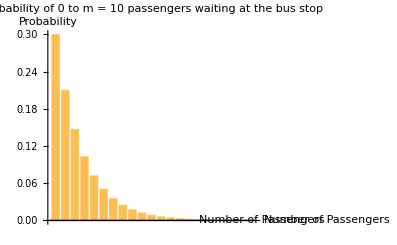

```mathematica
Clear[m] 
m=20;  
probabilities=Table[p[i],{i,0,m}];
BarChart[probabilities,AxesLabel->{"Number of Passengers","Probability"},PlotLabel->"Probability of 0 to m = 10 passengers waiting at the bus stop"]
```

#### Task III.B.2

We now limit the number of passengers at the bus stop to a maximum of m passengers (m-1 waiting places).  
For numerical values use the parameter set  𝒫_𝒬 from III.B.1, and m=6.
a) Change the Markov model from III.B.1 to take this limitation into considerations.
b) What kind of queuing model is this? (use Kendall’s notation)
c) Obtain the mean number of passengers, E[S], and the mean passenger waiting time at bus stop, E[W]. 
d) What is the probability of m passengers waiting at a bus stop? 
e) Plot the probability of 0-m passengers for the models in III.B.1 and in this task. 
f) Compare all results in this task with the corresponding results in III.B.1.

a) Since we have a upper limit, the model now stops at 6

b) M/M/1/6/FIFO

c) Using the same parameters from III.B.1 and m = 6, we get  and .

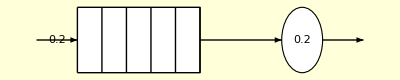
-Graphics- | 
Basic Properties | 
QueueNotation | M/M/1/6
ArrivalRate | 0.2
ServiceRate | 0.285714
UtilizationFactor | 0.673076
Throughput | 0.192308
ServiceChannels | 1
SystemCapacity | 6
InitialState | 0
Performance Measures | 
MeanSystemSize | 1.70512
MeanSystemTime | 8.86661
MeanQueueSize | 1.03204
MeanQueueTime | 5.36661

```mathematica
ClearAll[queue]
queue = QueueingProcess[λ, M, 1, 6]/. Subscript[𝒫, Q];
QueueProperties[queue]
```

d) The probability of m(=6) passengers waiting at the bus stop is 0.0385.

```mathematica
steadyStateProbs=StationaryDistribution[queue];
P=Probability[x==6,x \[Distributed] steadyStateProbs]
```

0.0384622

e) For an M/M/1/K system, the probability that  customers will be in the system when it is in a steady state is given by

Sum of probabilities when m = 6: 1.

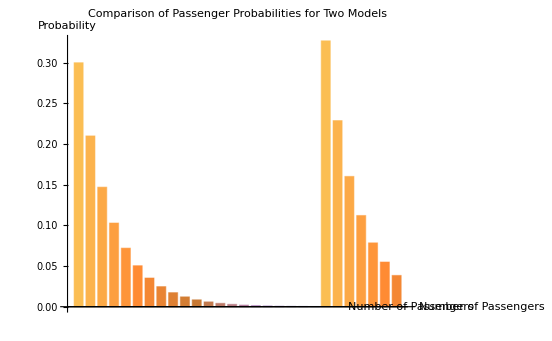

```mathematica
Clear[m] 
m=20;  
probabilities1=Table[p[i],{i,0,m}];

Clear[m,i]
m =6;
prob[n_]:=((1-A)A^n)/(1-A^{m+1});
probabilities2=Table[prob[i],{i,0,m}];
probabilities2= Flatten[probabilities2];
Print["Sum of probabilities when m = 6: ", Total[probabilities2]]

BarChart[{probabilities1, probabilities2},
AxesLabel->{"Number of Passengers","Probability"},
PlotLabel->"Comparison of Passenger Probabilities for Two Models",
BarSpacing->0.3 
]
```

f) If we compare the results from III.B.1 in this task we can see a few differences. From the performance measures provided in the tables below, we can see that the M/M/1 system without a capacity limit has higher overall performance measures compared to the M/M/1/6 system. This illustrates how the number of passengers and the time they spend in the system are reduced when a limit is introduced, since fewer people can wait because of the constrained capacity. The bar plot above helps to visualise why this is the case. In the unlimited scenario, the probabilities are more spread out across a wider range of passenger numbers. This illustrates that a higher number of passengers has a non-negligible probability, compared to the limited system where the probability distribution is more concentrated towards the lower passenger numbers. Since the sum of the probabilities when   adds up to one, we know that  - which aligns with our restriction.

```mathematica
-Graphics--Graphics-
```

### Task III.B.3

Obviously, the passengers can only enter the bus when a bus is at the bus stop. 
a) How will you change your state definition from the previous tasks to reflect that a bus is at a bus stop or not?
b) How many states does the model consists of when it is still only space for maximum m=6 passengers?
c) Use your state definition from a) and draw the Markov model on paper.
d) Show how you will defined the set of equation that are needed to obtain the steady state probabilities of the system states in the model.

a) To reflect the presence and absence of a bus, I will add a second variable to the state definition. This is represented as , where , and .

b) From previous we have 7 states, and since we have introduced two new states, bus/no bus, the new model will consist of  states. 

c)Markov model is illustrated below.  represents the arrival rate of passengers, while  represents the service rate of passengers.  represents the arrival rate of a bus, while  represents the departure rate of a bus. As you might notice, the passengers cannot leave a stop before a bus has arrived.
 -Graphics-
	
d) Showing the set of equations belonging to the top two and bottom two nodes, since the “pattern” repeats itself. Equation (1) has the same structure for node (6, 0), Equation (2) has the same structure for (6, 1),  Equation (3) has the same structure for all top nodes  that are not edge nodes, and Equation (4) has the same structure for all bottom nodes that are not edge nodes. 
	(I)   
	(2) 
	(3) 
	(4) 
	
The normalisation equation it critical as it ensures that the sum of all probabilities in the system equals one, which is a fundamental part of Markov Chains. This means that the system is in one of the possible states at any given time. 
	 = 1

#### Task III.B.4*

Now, implement the model you have defined above in Mathematica. You should use the “StateDiagrams.m” package that is explained in the “warm-up” on top of this notebook, and in the separate notebook provided on Blackboard.  
a) Define a transition intensity matrix of the model {a_(i,j)}=intensity of going from state i to state j. 
b) Use the operation modus (true/false) in the package to define states where there new passenger arrivals will be rejected (false), all other states are true.
c) Make labels reflecting the state definition you have chosen.
d) Plot the Markov model and compare it with the model you drew in III.B.3.  Note that the “operation modus” is indicated in the figure as circles when the state is defined as up (True) and square when it is down (False).
e) Obtain the steady state probabilities (p_i) of the system states in the model.
f) Use the steady state probabilities from e) to obtain the average number of passengers at the bus stop, and the probability that a passenger cannot enter the bus stop. 
g) Change α and β in 𝒫_𝒬 to α=0.02, β=0.12, and then to α=2, β=12.  Obtain the probability of a bus at the bus stop, and the properties in task f) above for these two cases and discuss similarities and differences.

a) Below you can see the transition intensity matrix of the model. Each column/row represents a unique state, e.g. column 1 and row 1 represents State 1. Each node represents a unique state, and is counted downwards,  going right, e.g. (0,0) is State 1, (0,1) is state State 2, and (1, 0) is State 3. The columns represent what are “lost” from a node, and the rows represent what is “given” to a node, e.g. column 2 and row 4 shows that State 2 “gives”  to State 4, which aligns with our model above.

```mathematica
ClearAll[β, α,λ, μ]

ℳ=ConstantArray[0,{14,14}];

For[i=0,i<=6,i++,(*For each state (i, 0)*)
If[i<6,ℳ[[2 i+1,2 i+3]]=λ];(*As long as Passengers < 6, a new can arrive, moving from State (i, 0) to State (i+1, 0) at rate λ*)
ℳ[[2 i+1,2 i+2]]=α; (*The bus can arrive the stop, moving from State (i, 0) to State (i, 1) at rate α*)
]; 

For[i=0,i<=6,i++,(*For each state (i, 1)*)
If[i<6,ℳ[[2 i+2,2 i+4]]=λ];(*As long as Passengers < 6, a new can arrive, moving from State (i, 1) to State (i+1, 1) at rate λ*)
If[i>0,ℳ[[2 i+2,2 i]]=μ];(*As long as Passengers > 0, someone can leave, moving from State (i, 1) to State (i-1, 1) at rate λ*)
ℳ[[2 i+2,2 i+1]]=β;(*The bus can leave the stop, moving from State (i, 1) to State (i, 0) at rate β*)
];

For[i=1,i<=14,i++,
ℳ[[i,i]]=-Total[ℳ[[i,All]]];(*Filling the diagonal with the sum of all params leaving the node*)
];

Matrix = Transpose[ℳ];(*Transposing because of Mathematica convensions*)
MatrixForm[Matrix]
```

(-α-λ | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
α | -β-λ | 0 | μ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | -α-λ | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | α | -β-λ-μ | 0 | μ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | -α-λ | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | α | -β-λ-μ | 0 | μ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | λ | 0 | -α-λ | β | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | λ | α | -β-λ-μ | 0 | μ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -α-λ | β | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | α | -β-λ-μ | 0 | μ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -α-λ | β | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | α | -β-λ-μ | 0 | μ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -α | β
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | α | -β-μ)

b) For the first twelve states,  there is room for another person, but for State 13 (6, 0) and State 14 (6, 1) the limit  is reached. Therefore those states are marked as False.

```mathematica
states = {True, True, True, True, True, True, True, True, True, True, True, True, False, False};
```

c) Labels as defined in the model above:

```mathematica
labels ={"0,0","0,1","1,0","1,1","2,0","2,1","3,0","3,1","4,0","4,1","5,0","5,1","6,0","6,1"};
```

d) The model is upside down from my drawing, but has the same properties.

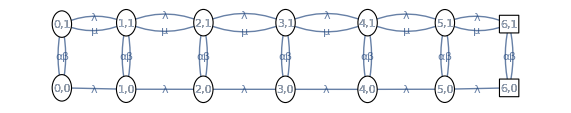

```mathematica
Show[PlotDiagram[Matrix, states, labels]]
```

e) The steady state probabilities are calculated below using the ProbStationary-function. As we can see, the total sum of the probabilities adds up to 1, which satisfies the normalisation condition.

```mathematica
ClearAll[β, α,λ, μ]
Subscript[𝒫, 𝒬]={λ->0.2,μ->2,α->0.2,β->1.2};
ps = ProbStationary[Matrix]/. Subscript[𝒫, 𝒬]
Total[ps]
```

{0.169852,0.0566172,0.152866,0.0226469,0.129087,0.0175513,0.108535,0.0146639,0.0912273,0.0123199,0.0766778,0.0103547,0.128897,0.00870325}

1.

f) To compute the average number of passengers at the bus stop, we multiply the number of passengers at the stop for each state with the steady state probability of that state and add them up. We can see that there is 2.5 passengers at the bus stop on average. The probability that a passenger cannot enter, is the sum of probabilities that the system is full, being in either State 13 (6, 0) or State 14 (6,1). The probability that a passenger cannot enter is 0.137.

```mathematica
statePassengerCounts = {0, 0, 1, 1, 2, 2, 3, 3, 4, 4, 5, 5, 6, 6};
averagePassengers = Total[ps * statePassengerCounts]
cannotEnterProbability = ps[[13]] + ps[[14]]
```

2.51334

0.137601

g) Since  and  are scaled in the same order, the probability of bus arrival does not change and stays the same in all cases, but since the params related to the passengers -  and  - stays the same, those values change. We can see from the calculations below, that as  and   increase, the passenger values decrease, since we have an increase in bus frequency. This leads to less crowing, and higher possibility of being allowed to enter the bus. As  and   decrease we  get the opposite results - less frequent bus arrivals, which leads to more crowded bus stops and smaller possibilities of free space.

```mathematica
ClearAll[β, α,λ, μ]
Print["α=0.2 & β=1.2"]
λ=0.2;
μ=2;
α=0.2;
β=1.2;
ps = ProbStationary[Matrix];
Print["State Probabilities: ", ps];
averagePassengers = Total[ps * statePassengerCounts];
Print["Average Passengers: ", averagePassengers]
cannotEnterProbability = ps[[13]] + ps[[14]]busProb;
Print["Probaility of not being allowed to enter: ", cannotEnterProbability ]
busProb;
Print["Bus arrival probability: ", busProb, "\n"]

ClearAll[β, α,λ, μ]
Print["α=0.02 & β=0.12"]
λ=0.2;
μ=2;
α=0.02;
β=0.12;
ps = ProbStationary[Matrix];
Print["State Probabilities: ", ps]
averagePassengers = Total[ps * statePassengerCounts];
Print["Average Passengers: ", averagePassengers]
cannotEnterProbability = ps[[13]] + ps[[14]]busProb;
Print["Probaility of not being allowed to enter: ", cannotEnterProbability ]
busProb;
Print["Bus arrival probability: ", busProb, "\n"]

ClearAll[β, α,λ, μ]
Print["α=2.0 & β=12.0"]
λ=0.2;
μ=2;
α=2.0;
β=12.0;
ps = ProbStationary[Matrix];
Print["State Probabilities: ", ps]
averagePassengers = Total[ps * statePassengerCounts];
Print["Average Passengers: ", averagePassengers]
cannotEnterProbability = ps[[13]] + ps[[14]]busProb;
Print["Probaility of not being allowed to enter: ", cannotEnterProbability ]
busProb;
Print["Bus arrival probability: ", busProb, "\n"]
```

α=0.2 & β=1.2

State Probabilities: {0.169852,0.0566172,0.152866,0.0226469,0.129087,0.0175513,0.108535,0.0146639,0.0912273,0.0123199,0.0766778,0.0103547,0.128897,0.00870325}

Average Passengers: 2.51334

Probaility of not being allowed to enter: 0.130141

Bus arrival probability: 0.142857

α=0.02 & β=0.12

State Probabilities: {0.052973,0.0971172,0.056344,0.015009,0.0551138,0.0071353,0.0534989,0.00622491,0.051893,0.00597238,0.0503317,0.00578654,0.536988,0.00561183}

Average Passengers: 4.14268

Probaility of not being allowed to enter: 0.53779

Bus arrival probability: 0.142857

α=2.0 & β=12.0

State Probabilities: {0.259911,0.0476504,0.191389,0.0307562,0.138569,0.0222145,0.100297,0.0160784,0.0725956,0.0116376,0.052545,0.00842332,0.0418355,0.00609683}

Average Passengers: 1.82221

Probaility of not being allowed to enter: 0.0427065

Bus arrival probability: 0.142857

#### Task III.B.5*

The models above, including the one in III.B.4, have weaknesses. 
a) In this task, go through all of models above, compare the results you have obtained, and discuss how you could improve to increase realism.
If you limited to use the Markov model we have used in III.B.4, suggest changes that can be done in this model to increase the realism.  
b) Sketch on paper how this model will look like. 
c) Optional: Implement in Mathematica if you think it is possible (and you are able to do so).
d) Optional: Obtain the same statistics as above and compare.

a) The models above are very simple compared to how the system works in the real word. The main weakness of these models, is that all of the parameters are constant. All of the parameters, β, α,λ, μ,  will vary throughout the day depending on traffic conditions and rush hour etc. To fix this, I would implement the parameters as  a function of time instead. The queue capacity is also a feature which does not align with the real world, because the bus stop itself has always room for more passengers, so I would also remove this limitation to increase realism. This leads us to another limitation of the model which is that the bus capacity is ignored. To take this into consideration,  I would add another state variable to illustrate if the passengers can board the bus (e.g. 0 = not full, 1 = full). This would give 4(n+1) states in total, where  is the limit of passengers at a stop. An additional remark, is that the system only considers that passengers leave the stop via the bus, and not because they ran out of patience etc.

b) In the new model i have chosen to add two new variables,  and , where  represents the rate a bus gets full, and  represents the rate passengers disembarks and the bus gets free seats. All variables are represented as a function of time, as the different rates can vary based on time of day, day of the week, stop popularity, route popularity, etc. Not sure if the model itself is 100% correct, but the idea behind it is;
	- Passengers can be generated all the time regardless of bus arrival and capacity. Represented as  .
	- Passengers can only get served when a bus is present and has capacity, (X, 1, 0). Represented as .
	- The bus arrives at the stop regardless of passenger count and bus capacity. Represented as .
	- The bus leaves a stop regardless of passenger count and bus capacity. Represented as .
	- One can only know if a bus is full when it has arrived at a stop, you don’t know before it has arrived. Represented as .
	- One can only know if a bus has free seats then is has arrived at a stop. Represented as .
-Graphics-

### Task III.C: The bus network of passenger*

In this task, you are going to use what is called open Jackson network, as described in Section 6.6. in the textbook.  
[[Mathematica has a function called QueueingNetworkProcess which can be applied, or you can do it on paper by hand.]]

#### Task III.C.1*

Passengers arrive at the bus stops according to a Poisson process with intensities λ_i (i=1,...,7).  The average service rate is M (from Task III.B.1.a)).  The capacity at the bus stop is unlimited. 
The next stop of a passenger is chosen randomly with a probability, p_(i,j)  ((i=1,...,7),(j=1,...,7), and at each stop there is a certain probability that a passenger leaves, p_i0,(i=1,...,7). 

 In this assignment you are going to make a Markov model that let you estimate the expected number of passengers waiting at each bus stop,  the expected total number of passengers in the system, and the expected time a passenger stays in the system.  For simplicity, we can ignore the driving time on the roads [or set a deterministic value and add this when you summarize the travel times, taking the probabilistic routing into account].

a) Which assumptions do you have to make in order to apply the Jackson queuing network modelling approach?
b) Make a queueing network (Ala Fig 6.22 in the textbook) of the eastbound (only) bus network with passengers arriving at all bus stops. At which bus stops can the passengers enter and exit the bus?
c) Determine the symbolic expressions of the total arrival intensity, Λ_i, to each bus stop ((i=1,...,7).  
d) Define your own numerical values of the parameters: the arrival intensities λ_i((i=1,...,7), the  service rates M_i, and all routing probabilities, p_(i,j)  ((i=1,...,7),(j=1,...,7).  Use this to determine the numerical values of the total arrival intensities Λ_i.  NOTE! Check if the stability condition is met for all bus stops, and adjust your parameters if not. 
e) What is the expected number of passengers at each each bus stop E[S_i]?
f) What is the expected number of passengers in the system, E[S]?
g) What is the expected waiting time at each bus stop, E[W_i]?
h) What is the expected time a passenger stays in the system (total travel time, with or without driving time), E[W]?
i) Discuss the results obtained by this model and from your simulations in Lab II.  Are the results very different? Explain why.

a) To be able to apply the Jackson queuing network modelling approach we need to assume the following:
	- The network consists of  open queuing systems, where each queue works as a M/M/n model
	- Customers arrive at a node from outside the system following a Poisson process, with arrival occurring randomly over time
	- Each node  contains  servers, where the service time follows an exponential distribution with parameter 
	- There is no limit to the number of customers that can wait at a node
	- After service at node , a customer is either routed to another node in  in the system with probability , or exits the network with probability . In other words, customers will either move to another node or leave the system after being served.

b) Queueing network of the eastbound bus network is illustrated below 
-Graphics-
c) 
	: The network is defined in a way that no passengers can enter the bus at the end stop. Therefore, the bus will be empty when arriving at the first stop on the route, making the total arrival rate equal to the boarding rate at that stop.
	: Same as above.
	: Same as above. 
	: Total arrival rate at a stop is given by the passenger intensity coming from the roads leading to it and the passengers at that current stop. 
	: Same as above.
	: Same as above. 
	: Same as above.
	
d)  Total arrival rates are calculated using randomly chosen values. Below you can see the total arrival rates.

```mathematica
ClearAll[λ, μ]
λ={0.3,0.1,0.3,0.2,0.6,0.6,0.6};
μ={2,1,0.9,0.6,0.8,1.7,2};
r = {1, 1, 1, 1, 1, 1, 1};
routes={
{0,0,0,0.3,0,0,0},
{0,0,0,0,0.4,0,0},
{0,0,0,0.1,0,0,0.7},
{0,0,0,0,0,0.8,0.2},
{0,0,0,0,0,0.3,0.4},
{0,0,0,0,0,0,0},
{0,0,0,0,0,0,0}
};
simulation = QueueingNetworkProcess[λ, routes,μ, r];

n=Length[λ];
totalArrivals=λ;
For[iter=1,iter<=100,iter++,totalArrivals=Table[λ[[i]]+Sum[routes[[j,i]]*totalArrivals[[j]],{j,1,n}],{i,1,n}];];
totalArrivals
```

{0.3,0.1,0.3,0.32,0.64,1.048,1.13}

e) Expected number of passengers at each bus stop is calculated below using Mathematica functions.

```mathematica
expecPass = Table[QueueProperties[{simulation, i}, "MeanSystemSize"], {i, 1,7}]
```

{0.176471,0.111111,0.5,1.14286,4.,1.60736,1.29885}

f) Expected total number of passengers in system can be calculated by taking the sum of expected number of passengers at each stop.

```mathematica
expecTotPass = Total[expecPass]
```

8.83665

g) Expected waiting time at each bus stop is calculated below using Mathematica functions.

```mathematica
expecWaitTimes = Table[QueueProperties[{simulation, i}, "MeanSystemTime"], {i, 1,7}]
```

{0.588235,1.11111,1.66667,3.57143,6.25,1.53374,1.14943}

h) Expected waiting time in the system is calculated below using Mathematica functions.

```mathematica
expecTotTime=Total[expecWaitTimes]
```

15.8706

i) The results from this lab aren’t extremely different from the results from Lab II, but I really don’t see a reason for them to be the same as last time. While I kept the same values for λ as in Lab II, the other parameters are different, and we are operating without a capacity. Another difference is that in this lab we consider the time it takes for passengers to board the bus, while we did not care about boarding time in the previous lab. I did not include a travel time in this simulation, which also differs from last time. In Lab II, the simulation followed multiple buses throughout a route, while in this lab we focus on all the possible stops from the last one. 

 -Graphics-

### Task III.D: Reflections*

#### Task III.D.1*

a) Have you used any AI tool? How and for what have you used it, and how useful did you find it
b) What have you learned from this assignment?  Challenges you have been facing, usability of the tool, relevance for you own interest and studies, etc.

a) For this lab I have used ChatGPT to help me understand tasks I found unclear, and discuss formulas and equations I have found online and in the book, which I needed some help with explaining. Since I am new to Mathematica,  I also used AI to help me with some code as well. I found it useful as some kind of discussion partner, but since I didn’t rely on it 100%, I often checked with other students or the assistants if there was something I was unsure of.  

b) From this assignment I have mostly learned A LOT of statistics. The statistics was also the main challenge with this lab, as it is a long time since I have worked with it. In the beginning it was also a bit challenging learning how  Mathematica worked, but that problem mostly disappeared after the first day, and when I got a better understanding of how it works, it turned out to be a really nice tool. oi As I said in Lab II I like this lab very much, and I like that it is a very realistic scenario, which makes it easier to understand what the different results actually are.